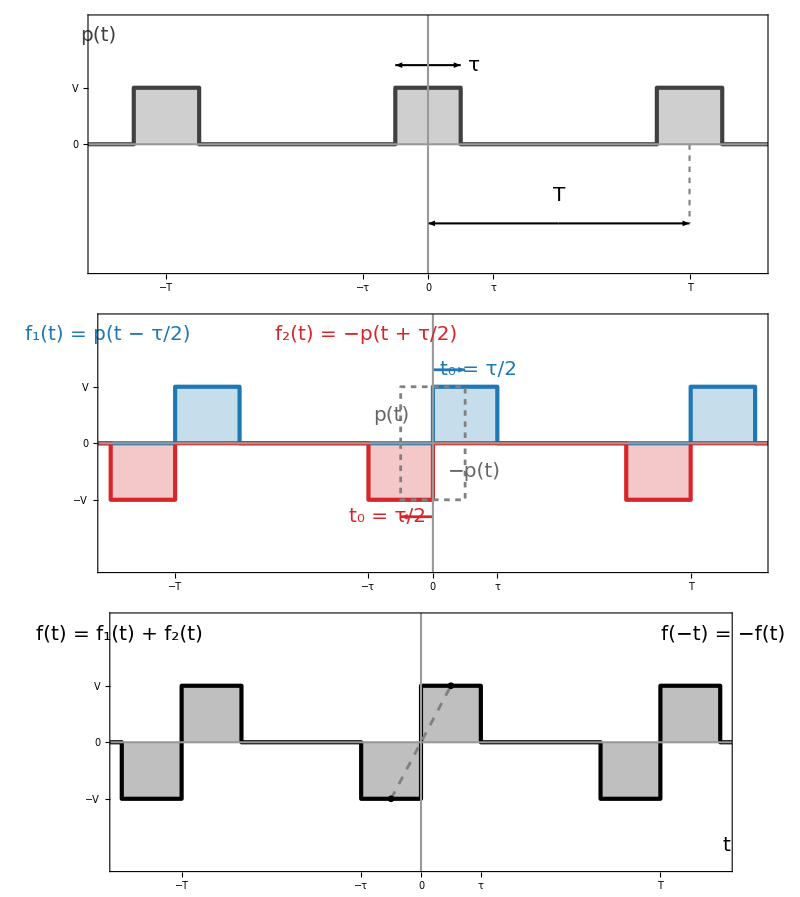

```mathematica
ClearAll[fs,vv,tau,per,blue,red,gray,ticksT,ticksY,shiftSegs,allSegs,signal,dblArrow,ghost,label,panel,specP,specF1,specF2,specF,g1,g2,g3,fig];

fs=20;      (*tamaño de fuente único*)
vv=1;       (*amplitud V*)
tau=1;      (*anchura τ*)
per=4;      (*período T (debe cumplirse τ<T/2)*)

blue=RGBColor[0.12,0.47,0.71];
red=RGBColor[0.84,0.15,0.16];
gray=GrayLevel[0.25];

(*Segmentos {inicio,fin,valor} de un período,replicados periódicamente*)
shiftSegs[spec_List,k_]:=Map[{#[[1]]+k per,#[[2]]+k per,#[[3]]}&,spec];
allSegs[spec_List]:=Flatten[Table[shiftSegs[spec,k],{k,-2,2}],1];

(*Señal:relleno suave+contorno grueso*)
signal[spec_List,col_]:=Module[{ss=allSegs[spec]},{{Opacity[0.25,col],EdgeForm[None],Map[Polygon[{{#[[1]],0},{#[[1]],#[[3]]},{#[[2]],#[[3]]},{#[[2]],0}}]&,Select[ss,#[[3]]!=0&]]},{col,AbsoluteThickness[3],Line[Flatten[Map[{{#[[1]],#[[3]]},{#[[2]],#[[3]]}}&,ss],1]]}}];

dblArrow[p1_List,p2_List]:={Arrow[{(p1+p2)/2,p1}],Arrow[{(p1+p2)/2,p2}]};

(*Pulso de referencia (sin desplazar) en trazo discontinuo*)
ghost[s_]:={GrayLevel[0.5],AbsoluteThickness[2],Dashing[{0.01,0.01}],Line[{{-tau/2,0},{-tau/2,s vv},{tau/2,s vv},{tau/2,0}}]};

(*Texto con tamaño fs;pos puede ser una lista o Scaled[...]*)
label[expr_,col_,pos_,off_List:{-1,0}]:=Text[Style[expr,fs,col],pos,off];

ticksT={{-per,Style["−T",fs]},{-tau,Style["−τ",fs]},{-tau/2,""},{0,Style["0",fs]},{tau/2,""},{tau,Style["τ",fs]},{per,Style["T",fs]}};
ticksY[spec_List]:=Map[{#[[1]],Style[#[[2]],fs]}&,spec];

panel[content_,ys_List,extra_List]:=Graphics[{content},PlotRange->{{-5,5},{-2.2,2.2}},PlotRangePadding->None,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicks->{{ticksY[ys],None},{ticksT,None}},GridLines->{{0},{0}},GridLinesStyle->Directive[GrayLevel[0.6],AbsoluteThickness[1.5]],Background->White,AspectRatio->0.34,ImagePadding->{{75,15},{45,10}},Epilog->extra];

(*Un período de cada señal:{inicio,fin,valor}*)
specP={{-per/2,-tau/2,0},{-tau/2,tau/2,vv},{tau/2,per/2,0}};
specF1={{-per/2,0,0},{0,tau,vv},{tau,per/2,0}};
specF2={{-per/2,-tau,0},{-tau,0,-vv},{0,per/2,0}};
specF={{-per/2,-tau,0},{-tau,0,-vv},{0,tau,vv},{tau,per/2,0}};

(*Panel 1:tren de pulsos p(t) con τ y T*)
g1=panel[signal[specP,gray],{{0,"0"},{vv,"V"}},{label["p(t)",gray,Scaled[{0.015,0.92}]],{Black,AbsoluteThickness[1.5],Arrowheads[0.018],dblArrow[{-tau/2,1.4},{tau/2,1.4}],dblArrow[{0,-1.4},{per,-1.4}]},{GrayLevel[0.5],AbsoluteThickness[1.5],Dashing[{0.01,0.01}],Line[{{per,0},{per,-1.4}}]},label["τ",Black,{tau/2+0.2,1.4}],label["T",Black,{per/2,-0.9},{0,0}]}];

(*Panel 2:f1 desplazado a la derecha y f2 invertido y desplazado a la izquierda*)
g2=panel[{signal[specF1,blue],signal[specF2,red],ghost[1],ghost[-1]},{{-vv,"−V"},{0,"0"},{vv,"V"}},{label[Row[{Subscript["f",1],"(t) = p(t − τ/2)"}],blue,Scaled[{0.015,0.92}]],label[Row[{Subscript["f",2],"(t) = −p(t + τ/2)"}],red,Scaled[{0.4,0.92}]],{blue,AbsoluteThickness[2],Arrowheads[0.018],Arrow[{{0,1.3},{tau/2,1.3}}]},label[Row[{Subscript["t",0]," = τ/2"}],blue,{tau/2+0.2,1.3}],{red,AbsoluteThickness[2],Arrowheads[0.018],Arrow[{{0,-1.3},{-tau/2,-1.3}}]},label[Row[{Subscript["t",0]," = τ/2"}],red,{-tau/2-0.2,-1.3},{1,0}],label["p(t)",GrayLevel[0.4],{-tau/2-0.15,0.5},{1,0}],label["−p(t)",GrayLevel[0.4],{tau/2+0.15,-0.5}]}];

(*Panel 3:suma,simetría impar*)
g3=panel[signal[specF,Black],{{-vv,"−V"},{0,"0"},{vv,"V"}},{label[Row[{"f(t) = ",Subscript["f",1],"(t) + ",Subscript["f",2],"(t)"}],Black,Scaled[{0.015,0.92}]],label["f(−t) = −f(t)",Black,Scaled[{0.985,0.92}],{1,0}],{GrayLevel[0.5],AbsoluteThickness[2],Dashing[{0.015,0.015}],Line[{{-tau/2,-vv},{tau/2,vv}}]},{Black,PointSize[0.012],Point[{{-tau/2,-vv},{tau/2,vv}}]},label["t",Black,Scaled[{0.99,0.1}],{1,0}]}];

fig=GraphicsColumn[{g1,g2,g3},Spacings->0,Background->White,ImageSize->800]
```

```mathematica
Export["T2_P2.png",fig,ImageResolution->300]
```

T2_P2.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["T2_P2.png"]]]
```